```mathematica
R1 = 400;
c1 = 10^-7;
L1=10^-2;
```

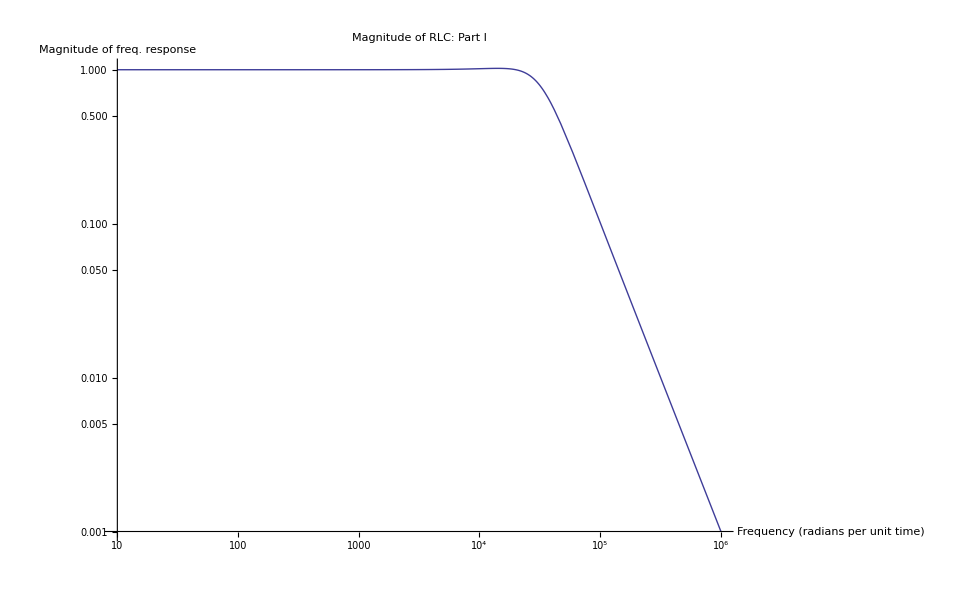

```mathematica
LogLogPlot[Abs[1/(ⅈ *w *R1*c1+(1-w^2 *L1 *c1))],{w,10,10^6},AxesLabel->{"Frequency (radians per unit time)","Magnitude of freq. response"},PlotLabel->"Magnitude of RLC: Part I"]
```

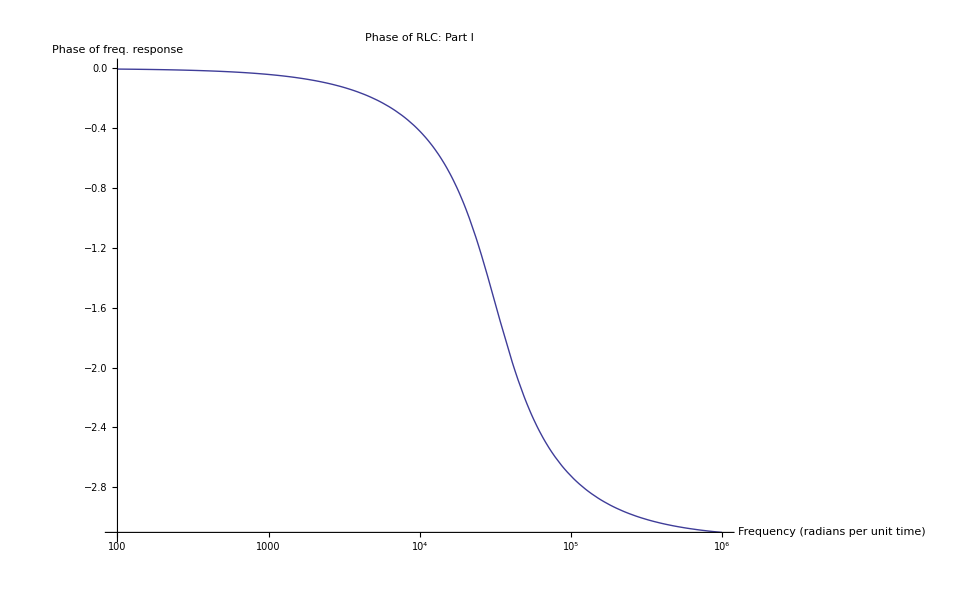

```mathematica
LogLinearPlot[Arg[1/(ⅈ *w *R1*c1+(1-w^2 *L1 *c1))],{w,10^2,10^6},AxesLabel->{"Frequency (radians per unit time)","Phase of freq. response"},PlotLabel->"Phase of RLC: Part I"]
```

```mathematica
R2 = 50;
c2 = 10^-7;
L2=10^-2;
```

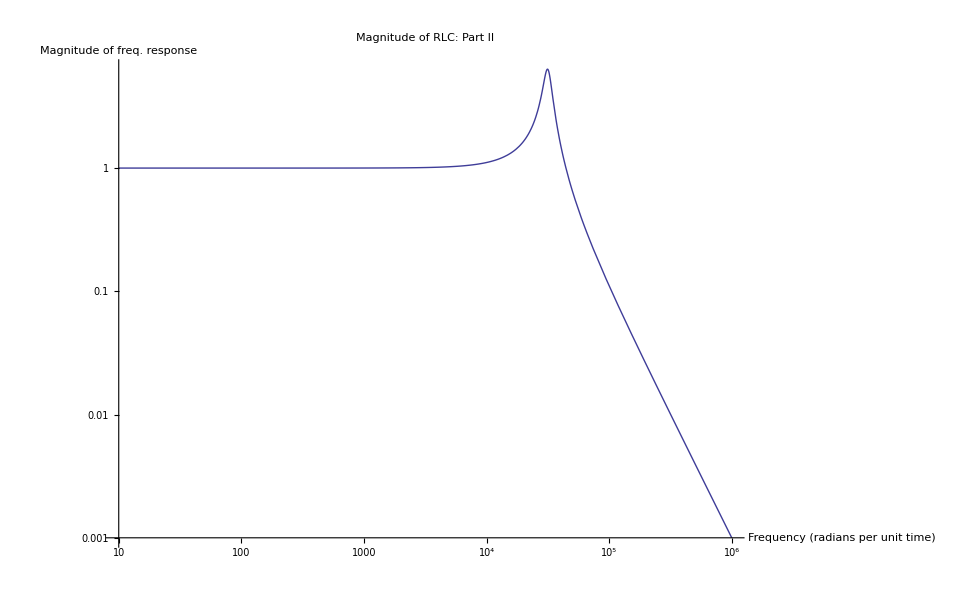

```mathematica
LogLogPlot[Abs[1/(ⅈ *w *R2*c2+(1-w^2 *L2 *c2))],{w,10,10^6},AxesLabel->{"Frequency (radians per unit time)","Magnitude of freq. response"},PlotLabel->"Magnitude of RLC: Part II"]
```

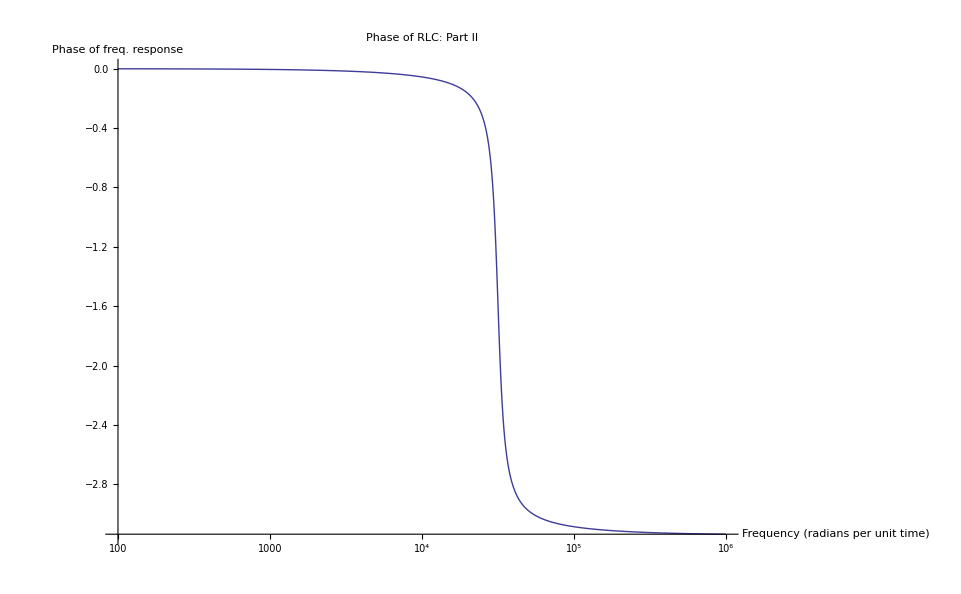

```mathematica
LogLinearPlot[Arg[1/(ⅈ *w *R2*c2+(1-w^2 *L2 *c2))],{w,10^2,10^6},AxesLabel->{"Frequency (radians per unit time)","Phase of freq. response"},PlotLabel->"Phase of RLC: Part II"]
```